# Implementer un variant de AdaBoost, comparer par Random Forest Nom: Zhibin LU

### Utiliser une approche “Boosting” sur cet ensemble de données (avec ou sans bruit). Discuter.

```mathematica
(*Je utilise un simple stump classifieur pour la modele de faible classifieur*)
stumpClassifieur[x_,dimen_,seuil_,direction_]:=Module[{},
If[x[[dimen]]≤seuil,-1*direction,1*direction]
];
(*calculer err pour les poids courant*)
calculErr[data_,poids_,dimen_,seuil_,direction_]:=Module[{e,i},
e=0.0;
For[i=1,i≤Length[data],i++,
If[stumpClassifieur[data[[i,1]],dimen,seuil,direction]≠ data[[i,2]],e+=poids[[i]]
];
];
e
];
(*calculer valeur z pour les poids courant*)
calculZ[data_,poids_,dimen_,seuil_,direction_,a_]:=Module[{z,i},
z=0.0;
For[i=1,i≤Length[data],i++,
If[stumpClassifieur[data[[i,1]],dimen,seuil,direction]≠ data[[i,2]],
z+=poids[[i]]*Exp[a],
z+=poids[[i]]*Exp[-a]
];
];
z
];
(*calculer les poids prochains*)
calculNextPoids[data_,poids_,dimen_,seuil_,direction_,a_,z_]:=Module[{npoids,i},
npoids={};
For[i=1,i≤Length[data],i++,
If[stumpClassifieur[data[[i,1]],dimen,seuil,direction]≠ data[[i,2]],
npoids=Append[npoids,(poids[[i]]*Exp[a])/z],
npoids=Append[npoids,(poids[[i]]*Exp[-a])/z]
];
];
npoids
];
```

```mathematica
(*chercher un classifieur fiable dans le but minizer error pour la fois courante*)
(*chaque fois, on uitlise la dimension differante que la fois dernier*)
chercheC[data_,poids_,cSet_]:=Module[{d,dimen,direct,direction,e,seuil,seuils,i,et,max,step},
(*dimen=If[Length[cSet]>0&&cSet[[Length[cSet],1]]==1,2,1];*)
e=0.6;
seuil=0;
dimen=0;
direct=0;
For[direction=-1,direction≤1,direction+=2,
For[d=1,d≤Length[data[[1,1]]],d++,

seuils=data[[All,1,d]];
For[i=1,i≤Length[seuils],i++,
et=calculErr[data,poids,d,seuils[[i]],direction ];
If[et<e,
e=et;
dimen=d;
direct=direction;
seuil=seuils[[i]];
];
];
];
];
{dimen,seuil,direct,e}
];
chercheC2[data_,poids_,cSet_]:=Module[{dimen,e,seuil,seuils,i,et,max,step},
dimen=If[Length[cSet]>0&&cSet[[Length[cSet],1]]==1,2,1];
e=0.6;
seuil=0;
(*
max=Max[data[[All,1,dimen]] ];
step=max/(2*Length[data])//N;
seuils=Table[i,{i,0,max,step}];*)
seuils=data[[All,1,dimen]];
For[i=1,i≤Length[seuils],i++,
et=calculErr[data,poids,dimen,seuils[[i]] ];
If[et<e,
e=et;
seuil=seuils[[i]];
];
];
{dimen,seuil,e}
];
```

```mathematica
(*calculer le taux d'erreur*)
calculTaux[data_,Ys_]:=Module[{i,err},
err=0;
For[i=1,i≤Length[data],i++,
If[Ys[[i]]≠ data[[i,2]],
err+=1;
];
];
err/Length[data]//N
];

(*Pour predire seulement une echantillon*)
AdaBoostPredire[x_,HCset_]:=Module[{t,sum},
sum=0;
For[t=1,t≤Length[HCset],t++,
sum+=HCset[[t,4]]*stumpClassifieur[x,HCset[[t,1]],HCset[[t,2]],HCset[[t,3]]];
];
Sign[sum]
];

(*Pour predire un set de donnees*)
comptePrediction[data_,HCset_]:=Module[{Ys,i},
Ys={};
For[i=1,i≤Length[data],i++,
Ys=Append[ Ys,AdaBoostPredire[data[[i,1]],HCset] ];
];
Ys
];

(*l'algorithme AdaBoost, epoque est le nombre de fois pour diviser les donnees*)
AdaBoostLu[data_,epoque_,showErr_]:=Module[{t,c,i,e,a,z,Dpoids,HCset,Ys},
Dpoids={Table[1/Length[data]//N,{i,1,Length[data]}]};
HCset={};
For[t=1,t≤epoque,t++,
c=chercheC[data,Dpoids[[t]],HCset];
e=c[[4]];
If[e≥0.5,Break[]];
a=0.5*(Log[1-e]-Log[e]);
z=calculZ[data,Dpoids[[t]],c[[1]],c[[2]],c[[3]],a ];
Dpoids=Append[Dpoids,calculNextPoids[data,Dpoids[[t]],c[[1]],c[[2]],c[[3]],a,z]];
HCset=Append[HCset,{c[[1]],c[[2]],c[[3]],a}];
If[showErr==1,
Ys=comptePrediction[data,HCset];
Print["Epoque=",t," taux d'erreur=",calculTaux[data,Ys]];
];
];
HCset
];
```

```mathematica
(*produire les donnees*)
data={};
Do[x=RandomReal[];y=RandomReal[];data=Join[data,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->1,{x,y}->-1]}],{500}];
dataerreur={};
Do[x=RandomReal[];y=RandomReal[];dataerreur=Join[dataerreur,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->-1,{x,y}->1]}],{50}];
trainingset=Join[data,dataerreur];
trainingset=data;
data={};
Do[x=RandomReal[];y=RandomReal[];data=Join[data,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->1,{x,y}->-1]}],{500}];
testset=data;
```

```mathematica
g1=ListPlot[{Pick[trainingset,trainingset[[All,2]],1],Pick[trainingset,trainingset[[All,2]],-1]},AspectRatio->1];
g2=ListPlot[{Pick[testset,testset[[All,2]],1],Pick[testset,testset[[All,2]],-1]},AspectRatio->1];
Show[g1,g2,cercle]
```

-Graphics-

```mathematica
(*commencer entrainer la modele*)
HCset=AdaBoostLu[trainingset,80,1];
Print["Length of Hight Classifieur=",Length[HCset]]
```

Epoque=1 taux d'erreur=0.336

Epoque=2 taux d'erreur=0.336

Epoque=3 taux d'erreur=0.26

Epoque=4 taux d'erreur=0.356

Epoque=5 taux d'erreur=0.224

Epoque=6 taux d'erreur=0.224

Epoque=7 taux d'erreur=0.188

Epoque=8 taux d'erreur=0.252

Epoque=9 taux d'erreur=0.178

Epoque=10 taux d'erreur=0.218

Epoque=11 taux d'erreur=0.14

Epoque=12 taux d'erreur=0.14

Epoque=13 taux d'erreur=0.124

Epoque=14 taux d'erreur=0.144

Epoque=15 taux d'erreur=0.1

Epoque=16 taux d'erreur=0.128

Epoque=17 taux d'erreur=0.09

Epoque=18 taux d'erreur=0.114

Epoque=19 taux d'erreur=0.092

Epoque=20 taux d'erreur=0.08

Epoque=21 taux d'erreur=0.072

Epoque=22 taux d'erreur=0.064

Epoque=23 taux d'erreur=0.056

Epoque=24 taux d'erreur=0.05

Epoque=25 taux d'erreur=0.114

Epoque=26 taux d'erreur=0.038

Epoque=27 taux d'erreur=0.074

Epoque=28 taux d'erreur=0.05

Epoque=29 taux d'erreur=0.05

Epoque=30 taux d'erreur=0.034

Epoque=31 taux d'erreur=0.032

Epoque=32 taux d'erreur=0.032

Epoque=33 taux d'erreur=0.022

Epoque=34 taux d'erreur=0.05

Epoque=35 taux d'erreur=0.024

Epoque=36 taux d'erreur=0.036

Epoque=37 taux d'erreur=0.024

Epoque=38 taux d'erreur=0.038

Epoque=39 taux d'erreur=0.028

Epoque=40 taux d'erreur=0.02

Epoque=41 taux d'erreur=0.03

Epoque=42 taux d'erreur=0.012

Epoque=43 taux d'erreur=0.016

Epoque=44 taux d'erreur=0.018

Epoque=45 taux d'erreur=0.024

Epoque=46 taux d'erreur=0.018

Epoque=47 taux d'erreur=0.018

Epoque=48 taux d'erreur=0.024

Epoque=49 taux d'erreur=0.012

Epoque=50 taux d'erreur=0.012

Epoque=51 taux d'erreur=0.016

Epoque=52 taux d'erreur=0.022

Epoque=53 taux d'erreur=0.016

Epoque=54 taux d'erreur=0.016

Epoque=55 taux d'erreur=0.018

Epoque=56 taux d'erreur=0.01

Epoque=57 taux d'erreur=0.018

Epoque=58 taux d'erreur=0.012

Epoque=59 taux d'erreur=0.022

Epoque=60 taux d'erreur=0.014

Epoque=61 taux d'erreur=0.018

Epoque=62 taux d'erreur=0.018

Epoque=63 taux d'erreur=0.018

Epoque=64 taux d'erreur=0.018

Epoque=65 taux d'erreur=0.016

Epoque=66 taux d'erreur=0.01

Epoque=67 taux d'erreur=0.022

Epoque=68 taux d'erreur=0.014

Epoque=69 taux d'erreur=0.014

Epoque=70 taux d'erreur=0.012

Epoque=71 taux d'erreur=0.018

Epoque=72 taux d'erreur=0.01

Epoque=73 taux d'erreur=0.004

Epoque=74 taux d'erreur=0.01

Epoque=75 taux d'erreur=0.004

Epoque=76 taux d'erreur=0.01

Epoque=77 taux d'erreur=0.004

Epoque=78 taux d'erreur=0.01

Epoque=79 taux d'erreur=0.004

Epoque=80 taux d'erreur=0.004

Length of Hight Classifieur=80

```mathematica
HCset
```

{{2,0.765385,-1,0.340585},{2,0.367183,1,0.29085},{1,0.999815,1,0.209181},{1,0.814843,-1,0.317649},{1,0.27198,1,0.296182},{1,0.999815,1,0.312042},{2,0.719942,-1,0.262605},{2,0.23097,1,0.248852},{1,0.999815,1,0.257908},{1,0.155993,1,0.284468},{1,0.636777,-1,0.271916},{1,0.999815,1,0.26322},{2,0.136287,1,0.24001},{2,0.632954,-1,0.187726},{1,0.999815,1,0.214602},{1,0.132935,1,0.258549},{1,0.999815,1,0.196312},{1,0.860836,-1,0.286799},{1,0.999815,1,0.212298},{2,0.872453,-1,0.263694},{1,0.999815,1,0.203612},{2,0.136287,1,0.262794},{1,0.999815,1,0.190846},{1,0.217322,1,0.2478},{1,0.75663,-1,0.180652},{1,0.999815,1,0.224742},{2,0.848848,-1,0.243791},{1,0.999815,1,0.176496},{2,0.246471,1,0.234576},{1,0.327611,1,0.181476},{1,0.999815,1,0.173552},{1,0.860836,-1,0.264293},{1,0.999815,1,0.1931},{2,0.872453,-1,0.216892},{1,0.999815,1,0.171395},{1,0.104979,1,0.223278},{1,0.999815,1,0.182072},{1,0.886408,-1,0.200771},{1,0.999815,1,0.166889},{2,0.108212,1,0.203639},{1,0.999815,1,0.168857},{2,0.80239,-1,0.195341},{1,0.999815,1,0.117862},{1,0.132935,1,0.198498},{1,0.999815,1,0.149813},{1,0.758518,-1,0.207175},{2,0.246471,1,0.153389},{1,0.999815,1,0.180887},{2,0.748206,-1,0.191653},{1,0.307017,1,0.177552},{1,0.999815,1,0.136009},{2,0.136287,1,0.199904},{1,0.999815,1,0.145766},{1,0.886408,-1,0.200597},{1,0.999815,1,0.166769},{2,0.884182,-1,0.184534},{1,0.999815,1,0.155553},{1,0.104979,1,0.19199},{1,0.999815,1,0.160799},{1,0.828115,-1,0.1802},{2,0.333028,1,0.131494},{1,0.999815,1,0.158543},{2,0.884182,-1,0.172797},{1,0.999815,1,0.147153},{1,0.148044,1,0.176962},{2,0.59786,-1,0.130088},{1,0.999815,1,0.146628},{2,0.202861,1,0.194726},{1,0.698281,-1,0.130336},{1,0.999815,1,0.160168},{1,0.27198,1,0.188159},{1,0.594514,-1,0.125742},{2,0.764923,-1,0.118808},{1,0.999815,1,0.150262},{2,0.108212,1,0.183689},{1,0.999815,1,0.154955},{1,0.104979,1,0.160728},{1,0.999815,1,0.138329},{1,0.886408,-1,0.162754},{1,0.999815,1,0.139824}}

```mathematica
Ytrain=comptePrediction[trainingset,HCset];
Ytest=comptePrediction[testset,HCset];
calculTaux[trainingset,Ytrain]
calculTaux[testset,Ytest]
```

0.004

0.036

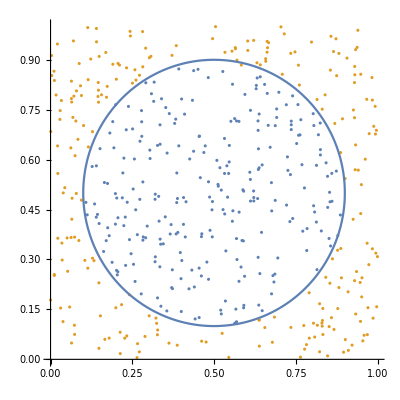

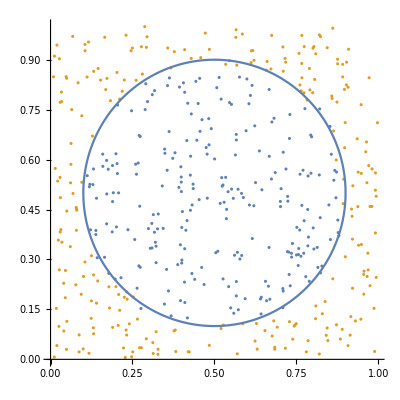

-Graphics-

```mathematica
pseta={};
psetb={};
For[i=1,i≤Length[trainingset],i++,
If[ Ytrain[[i]]==1,
pseta=Append[pseta,trainingset[[i,1]] ],
psetb=Append[psetb,trainingset[[i,1]] ]
];
];
psetc={};
psetd={};
For[i=1,i≤Length[testset],i++,
If[ Ytest[[i]]==1,
psetc=Append[psetc,testset[[i,1]] ],
psetd=Append[psetd,testset[[i,1]] ]
];
];
preditG1=ListPlot[{pseta,psetb},AspectRatio->1];
preditG2=ListPlot[{psetc,psetd},AspectRatio->1];
(*training data*)
Show[preditG1,cercle]
(*test data*)
Show[preditG2,cercle]
(*orignial*)
Show[g1,g2,cercle]
```

```mathematica
(*comparer AdaBoost et RandomForet *)
résultat={};
Do[
data={};
Do[x=RandomReal[];y=RandomReal[];data=Join[data,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->1,{x,y}->-1]}],{500}];
dataerreur={};
Do[x=RandomReal[];y=RandomReal[];dataerreur=Join[dataerreur,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->-1,{x,y}->1]}],{50}];
trainingset=Join[data,dataerreur];
trainingset=data;
data={};
Do[x=RandomReal[];y=RandomReal[];data=Join[data,{If[(x-0.5)^2+(y-0.5)^2<0.16,{x,y}->1,{x,y}->-1]}],{500}];
testset=data;

c=Classify[trainingset, Method-> {"RandomForest","TreeNumber"->10}];
ar=ClassifierMeasurements[c,testset,"Error"];

HCset=AdaBoostLu[trainingset,80,0];
Ytest=comptePrediction[testset,HCset];
ab=calculTaux[testset,Ytest];
résultat=Append[résultat,{ar,ab}];
Print[{ar,ab}],10]
```

{0.03,0.044}

{0.052,0.042}

{0.06,0.054}

{0.038,0.046}

{0.044,0.046}

{0.038,0.036}

{0.058,0.054}

{0.056,0.054}

{0.044,0.054}

{0.038,0.03}

```mathematica
data1=résultat[[All,1]]
data2=résultat[[All,2]]
TTest[{data1,data2}]
```

{0.03,0.052,0.06,0.038,0.044,0.038,0.058,0.056,0.044,0.038}

{0.044,0.042,0.054,0.046,0.046,0.036,0.054,0.054,0.054,0.03}

0.962258

Conclusion:
J’ai implémenté l’algorithme de AdaBoost moi-même dans Mathematica, en utilisant un faible classifieur de stump. J’ai comparé AdaBoost et RandomForest par 500 training data plus 50 bruits et 500 test data en marchant 10 fois.
Selon le résultat, P-valeur >> 0.01, donc les méthode de AdaBoost et de RandomForest ne sont pas évidemment différents .